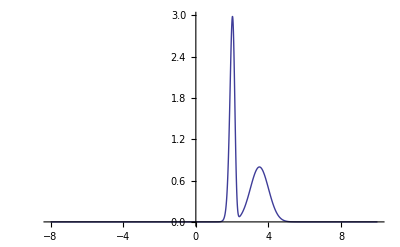

```mathematica
Plot[Evaluate[A1/(√(2π σ1^2))Exp[-(Exp[y]-Exp[y1])^2/(2 σ1^2)]Exp[y]+A2/(√(2π σ2^2))Exp[-(y-y2)^2/(2 σ2^2)]/.{A1->1,A2->1,σ1->1,σ2->0.5,y1->2.0,y2->3.5}],{y,-8,10},AxesOrigin->{0,0},   PlotRange->All]
```

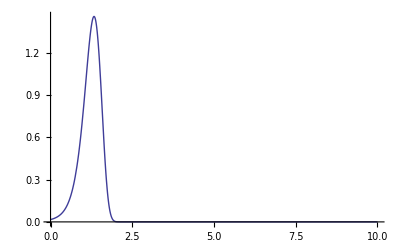

```mathematica
Plot[Evaluate[1/(√(2π σ2^2))Exp[-(Exp[y]-y2)^2/(2 σ2^2)]Exp[y]/.{C1->1.1379005294233837,C2->0.05,A1->0.4,σ2->1,y2->3.5199485433578344}],{y,0,10},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
fitFunc
```

{(A1 ⅇ^(y-((ⅇ^y-ⅇ^y1)^2)/(2 σ1^2)))/(√(2 π) √(σ1^2))+(A2 ⅇ^(-(y-y2)^2/(2 σ2^2)))/(√(2 π) √(σ2^2)),{C2>0,σ2>0}}

```mathematica
fitParams
```

{{A1,1},{A2,1},{σ1,1},{σ2,1},{y1,2.},{y2,3.5}}